```mathematica
Eqt4 = f^4*xbt + f^3*(1-f)*xi + f^2*(1-f)*xi+f*(1-f)*xi+(1-f)*xi
```

f^4 xbt+(1-f) xi+(1-f) f xi+(1-f) f^2 xi+(1-f) f^3 xi

```mathematica
Eqt5 = f^5*xbt +f^4*(1-f)*xi + f^3*(1-f)*xi + f^2*(1-f)*xi+f*(1-f)*xi+(1-f)*xi
```

f^5 xbt+(1-f) xi+(1-f) f xi+(1-f) f^2 xi+(1-f) f^3 xi+(1-f) f^4 xi

```mathematica
FullSimplify[Eqt4]
```

f^4 (xbt-xi)+xi

```mathematica
FullSimplify[Eqt5]
```

f^5 (xbt-xi)+xi

```mathematica
f^n*f^n
```

f^(2 n)

```mathematica
D[D[(xb-x)^2,x],x]
D[D[x*(xb - x),x],x]
D[D[x^2,x],x]
```

2

-2

2

```mathematica
var = f^(2n)*σ^2-2*f^n*σ^2 + σ^2
```

σ^2-2 f^n σ^2+f^(2 n) σ^2

```mathematica
FullSimplify[var]
```

(-1+f^n)^2 σ^2

```mathematica
(f^n*(xb-x)+x)^2
```

(x+f^n (-x+xb))^2

```mathematica
Expand[%]
```

x^2-2 f^n x^2+f^(2 n) x^2+2 f^n x xb-2 f^(2 n) x xb+f^(2 n) xb^2

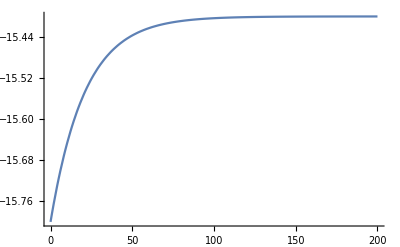

```mathematica
DiffIncorp[f_,xi_,T_] :=
NDSolve[
{xb'[t] == f*xb[t] + (1-f)*xi - xb[t],
xb[0]==-15.8},
xb,{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{f=0.952381,xi=-15.4,T=200},

Traj = Evaluate[xb[t]/.DiffIncorp[f,xi,T]];
Plot[Traj,{t,0,T},PlotRange->All]

]
```

```mathematica
Solve[0 == f*xbstar + (1-f)*xi - xbstar, xbstar]
```

{{xbstar→xi}}

```mathematica
Remove["Global`*"]
```

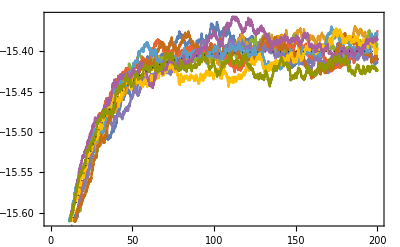

```mathematica
T = 200;
Iterations = 10;
IP[f_,xbar_,sigma_,x0_] := ItoProcess[
ⅆxb[t]==f*xb[t]*ⅆt+(1-f)*(xbar*ⅆt + sigma*ⅆw[t]) - xb[t]*ⅆt,
xb[t],{xb,x0},t,w\[Distributed]WienerProcess[]];
stochsol[f_,xbar_,sigma_,x0_] :=
RandomFunction[IP[f,xbar,sigma,x0],{0,T,0.05},Iterations,Method-> "KloedenPlatenSchurz"];

With[{f=0.952381,xbar=-15.4,sigma =0.1,x0=-15.8},
TD = stochsol[f,xbar,sigma,x0]["PathComponents"];
Show[{
ListLinePlot[stochsol[f,xbar,sigma,x0],Frame->True],
Plot[ⅇ^((-1+f) t) (x0-xbar)+xbar,{t,0,T},PlotRange->All,PlotStyle->{Black,Thick,Dotted}]
}]
]
```

```mathematica
ExpIP = Mean[IP[f,xbar,sigma,x0][t]]
VarIP = Variance[IP[f,xbar,sigma,x0][t]]
```

ⅇ^((-1+f) t) (x0-xbar)+xbar

1/2 (-1+ⅇ^(2 (-1+f) t)) (-1+f) sigma^2

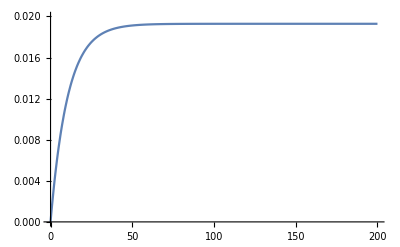

```mathematica
With[{f=0.952381,sigma=0.9},
Plot[1/2 (-1+ⅇ^(2 (-1+f) t)) (-1+f) sigma^2,{t,0,T},PlotRange->{0,0.02}]
]
```

```mathematica
Limit[ExpIP/.{f->0.952381},t -> Infinity]
```

xbar

```mathematica
Limit[VarIP/.{f->0.952381},t->Infinity]
```

0.0238095 sigma^2

```mathematica
Sqrt[%]
```

0.138873